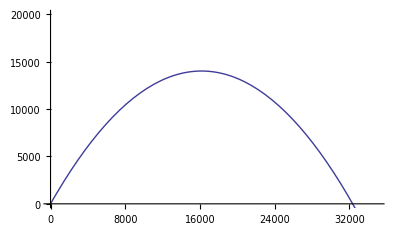

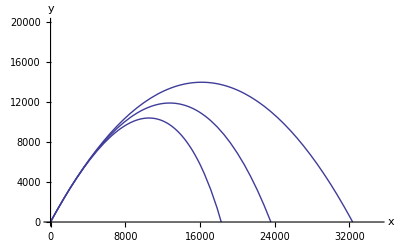

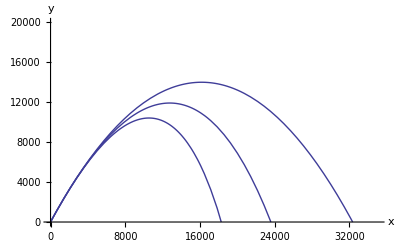

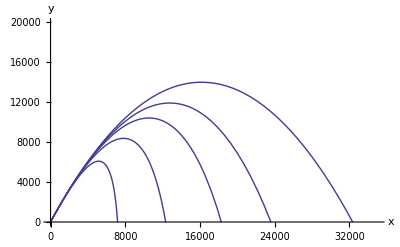

```mathematica
Remove["Global`*"]
solnx=DSolve[{x''[t]+k x'[t]==0,x[0]==0,x'[0]==U},x[t],t][[1]]//FullSimplify;
solny=DSolve[{y''[t]+k y'[t]+g==0,y[0]==0,y'[0]==V},y[t],t][[1]] //FullSimplify;
(*y is a variable not a function*)
y=y[t]/.solny;
x1=x[t]/.solnx;
(*Try to create t[x]*)
(*have a solution for x[t] and call it x and invert it for t*)
solnt=Solve[x==x[t]/.solnx,t][[1]];
(*create y[x] which is the y fro above with all of the t's switched to solutions*)
(*y[x_]=y/.solnt you can't use y as variable name and function*) 
ynew[k_,x_]=y/.solnt/.C[1]->0;
(*************************************************************)
(*Make the plots*)
(*Define parameters*)
g=9.8;
v0=605;
θ=60 Degree;
U=v0 Cos[θ];
V=v0 Sin[θ];
klist={10^(-7),0.005,0.01,0.02,0.04,0.08};


ParametricPlot[{x1,y}/.k->klist[[1]],{t,0,120},PlotRange->{{0,35000},{0,20000}}]


xlo=0;
xhi=35000;

myplot[k_]:=Plot[ynew[k,x],{x,xlo,xhi},PlotRange->{{0,35000},{0,20000}},AxesLabel->{"x","y"},DisplayFunction->Identity]
Show[myplot[{10^(-7),0.005,0.01}]]
Show[myplot[10^-7],myplot[0.005],myplot[0.01]]
Show[Table[myplot[klist[[i]]],{i,1,5}]]
```